```mathematica
Clear["Global`*"]
```

```mathematica
llambda=32;                    
nqList={3,4,5};             
E0ref=0.85974269044550901935596;
```

```mathematica
(*Hamiltonian using QuFoTr*)
HamiltonianJLP[ns_,phiMax_, llambda_]:=Module[
{deltaPhi,beta,phi,phi2,kmax,deltaK,betak,k,F,Pik2,Piphi2,H},

deltaPhi=2 phiMax/(ns-1);
beta=Range[0,ns-1];
phi=-phiMax+beta deltaPhi;
phi2=DiagonalMatrix[phi^2];(*diagonal phi squared matrix in the field space*)

kmax=Pi/deltaPhi;
deltaK=2 Pi/(deltaPhi ns);
betak=Range[0,ns-1];
k=-kmax+betak deltaK;

F=Exp[-I Outer[Times,k,phi]]/Sqrt[ns]; (*creates a unitary Fourier matrix that transforms between the field basis and the momentum basis F phi=K*)

Pik2=DiagonalMatrix[k^2];(*diagonal pi squared matrix in momentum space*)

Piphi2=ConjugateTranspose[F].Pik2.F;(*pi squared matrix in field space*)

H=0.5 (phi2+Piphi2) + (llambda/24) MatrixPower[phi2,2];(*Hamiltonian*)

(*might end up being slightly none hermitian because computers so:*)
H=0.5 (H+ConjugateTranspose[H]);

{H,phi}
];

(*Precision Function*)

FindPrecisionE0[method_,ns_,phiMax_,llambda_,E0ref_]:=Module[
{H,e0},
{H,_}=Which[method=="JLP",HamiltonianJLP[ns,phiMax,llambda],True,Return[$Failed,Module]];
e0=First@Sort@Re@Eigenvalues[H];(*ground state energy*)
100 Abs[(e0-E0ref)/E0ref]       (*returns percentage precision*)];

(*Automated results get*)

ComputeResultsE0[method_,nqList_,phiMaxValues_,llambda_, E0ref_]:=Module[
{results=Association[],ns},

Print["Computing reference E0 llambda = ",llambda];


Print["Reference E0 = ",E0ref];
Do[ns=2^nq;
Print["→ Calculating for nQ = ",nq," (ns = ",ns,")"];
results[nq]=Table[{phiMax,FindPrecisionE0[method,ns,phiMax,llambda,E0ref]},{phiMax,phiMaxValues}],{nq,nqList}];
results];

(*Plotting Functions*)

SetAttributes[SingleSetResults,HoldFirst];

SingleSetResults[results1_,nqList_]:=Module[
{res,colorList,styleList,allCurves,legendLabels,plt,name1},

name1=SymbolName[Unevaluated[results1]];
res=Evaluate[results1];

colorList=Table[ColorData["Rainbow"][x],{x,0,1,1/(Length[nqList]-1)}]; (*rainbow color map*)
styleList=Table[{colorList[[i]],Thick,Dashed},{i,Length[nqList]}];

(*build one curve per nQ*)
allCurves=Flatten[Table[
Style[Table[{res[nqList[[m]]][[i,1]],res[nqList[[m]]][[i,2]]},
{i,Length[res[nqList[[m]]]]}],
Sequence@@styleList[[m]]],
{m,Length[nqList]}],1];

legendLabels=Table["nQ = "<>ToString[nqList[[m]]],{m,Length[nqList]}];

plt=ListLogPlot[allCurves,Joined->True,Frame->True,FrameLabel->{"phi Max","Precision (%)"},PlotLegends->Placed[LineLegend[colorList,legendLabels,LegendMarkerSize->30],Below],GridLines->Automatic,PlotLabel->Style[name1<>"λ = 32 (Ground State Precision)",16],ImageSize->Large,PlotRange->All];
plt];
```

Computing reference E0 llambda = 32

Reference E0 = 0.859742690445509019356

→ Calculating for nQ = 3 (ns = 8)

Set::nosym: _ does not contain a symbol to attach a rule to.

General::stop: Further output of Set::nosym will be suppressed during this calculation.

→ Calculating for nQ = 4 (ns = 16)

→ Calculating for nQ = 5 (ns = 32)

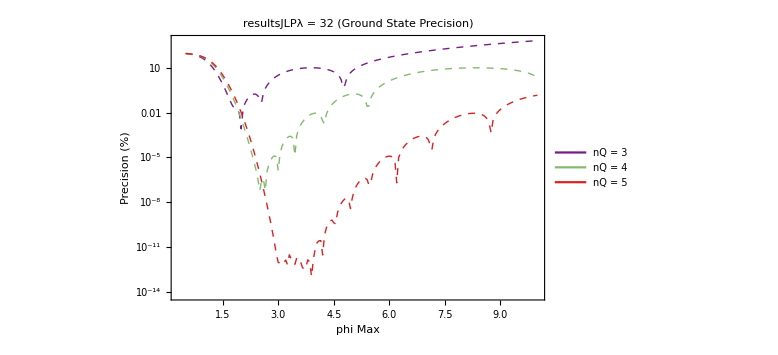

```mathematica
phiMaxValues=Range[0.5,10,0.05];  (*phi range sweep*)
resultsJLP=ComputeResultsE0["JLP",nqList,phiMaxValues,llambda, E0ref];
plotsingleresultsJLP=SingleSetResults[resultsJLP,nqList];
plotsingleresultsJLP
```

```mathematica
(*build creation and annihilation operators*)
LadderOps[ns_]:=Module[
{a,ad},

a=ConstantArray[0,{ns,ns}];
Do[a[[n,n+1]]=Sqrt[n],{n,1,ns-1}];(*<n|a|n+1> =sqrt(n)*)

ad=Transpose[a];
{a,ad}
];

(*make the Hamiltonian in the HO basis*)
HamiltonianHO[ns_,omega_, llambda_]:=Module[
{a,ad,phiOp,piOp,H},

{a,ad}=LadderOps[ns];

phiOp=(a+ad)/Sqrt[2.0*omega];(*diagonal omega operator in field space*)
piOp=I*Sqrt[omega/2.0]*(ad-a);(*momentum operator in momentum space*)
H=0.5 (piOp.piOp+phiOp.phiOp)+(llambda/24) MatrixPower[phiOp,4];

H=0.5 (H+ConjugateTranspose[H]);(*ensure Hermitian*)
{H,Null}
];

(*precision function for HO basis identical metric to previous but scans over omega instead of phi max*)
FindPrecisionHO[ns_,omega_,llambda_,E0ref_]:=Module[
{H,e0},

{H,_}=HamiltonianHO[ns,omega,llambda];

e0=First@Sort@Re@Eigenvalues[H];

100 Abs[(e0-E0ref)/E0ref]  (*percent deviation from reference*)];

(*automated results collection for the HO basis*)
ComputeResultsHO[nqList_,omegaList_,llambda_,E0ref_]:=Module[
{results=Association[],ns},

Print["Computing HO results for llambda = ",llambda];
Print["Reference E0 = ",E0ref];

Do[ns=2^nq;
Print["→ Calculating for nQ = ",nq," (ns = ",ns,")"];
results[nq]=Table[
{omega,FindPrecisionHO[ns,omega,llambda,E0ref]},{omega,omegaList}],{nq,nqList}];
results];

(*plotting function for HO results*)
SetAttributes[SingleSetResultsHO,HoldFirst];

SingleSetResultsHO[resultsHO_,nqList_,scalar_]:=Module[
{res,colorList,styleList,allCurves,legendLabels,plt,name1, safePos},

name1=SymbolName[Unevaluated[resultsHO]];
res=Evaluate[resultsHO];

safePos[x_]:=If[x<=0,$MachineEpsilon,x];  (*keep log-scale happy*)

colorList=Table[ColorData["Rainbow"][x],{x,0,1,1/(Length[nqList]-1)}];
styleList=Table[{colorList[[i]],Thick,Solid},{i,Length[nqList]}];

allCurves=Flatten[
Table[Style[Table[{scalar*Sqrt[Power[2,nqList[[m]]]/safePos[res[nqList[[m]]][[i,1]]]],(*convert w to equivalent omega max axis:1.4 √(2 nQ)/w*) 
res[nqList[[m]]][[i,2]]},{i,Length[res[nqList[[m]]]]}],Sequence@@styleList[[m]]],{m,Length[nqList]}],1];

legendLabels=Table["nQ = "<>ToString[nqList[[m]]],{m,Length[nqList]}];

plt=ListLogPlot[allCurves,Joined->True,Frame->True,FrameLabel->{"effective phimax:("<>ToString[scalar]<>" √(2 nQ)/w)","Precision (%)"},PlotLegends->Placed[LineLegend[colorList,legendLabels,LegendMarkerSize->30],Below],GridLines->Automatic,PlotLabel->Style[name1<>" llambda = 32 (HO Basis)",16],ImageSize->Large,PlotRange->All];
plt];
```

Computing HO results for llambda = 32

Reference E0 = 0.859742690445509019356

→ Calculating for nQ = 3 (ns = 8)

Set::nosym: _ does not contain a symbol to attach a rule to.

General::stop: Further output of Set::nosym will be suppressed during this calculation.

→ Calculating for nQ = 4 (ns = 16)

→ Calculating for nQ = 5 (ns = 32)

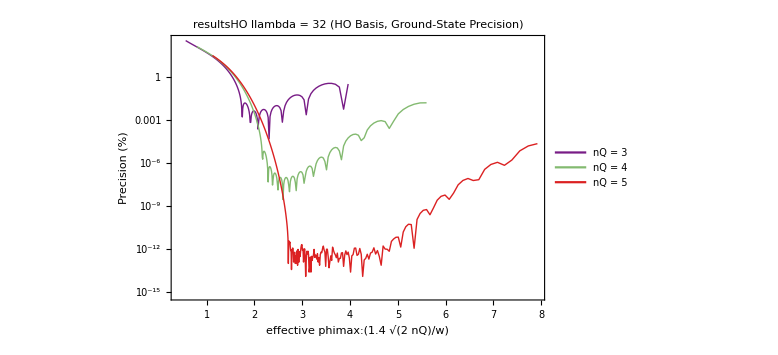

```mathematica
omegaList=Range[1,50,0.05];
(*compute and plot HO results*)
resultsHO=ComputeResultsHO[nqList,omegaList,llambda,E0ref];
plotHO=SingleSetResultsHO[resultsHO,nqList,1.4];
plotHO
```

```mathematica
CompareResultsSimple[resultsJLP_,resultsHO_,nqList_,scalar_]:=Module[
{resJLP,resHO,colorList,styleJLP,styleHO,allCurves,legendLabels,plt,safePos,getJLPVal},

resJLP=Evaluate[resultsJLP];
resHO=Evaluate[resultsHO];

safePos[x_]:=If[x<=0,$MachineEpsilon,x];(*avoid log(0)*)

(*handles both {phi max,err} and {phi max,{err1,…}} forms*)getJLPVal[data_,i_]:=Module[{val=data[[i,2]]},If[ListQ[val],safePos[val[[1]]],safePos[val]]];

colorList=Table[ColorData["Rainbow"][x],{x,0,1,1/(Length[nqList]-1)}];
styleJLP=Table[{colorList[[i]],Thick,Dashed},{i,Length[nqList]}];
styleHO=Table[{colorList[[i]],Thick,Solid},{i,Length[nqList]}];

allCurves=Flatten[Table[{

(*JLP dashed curves*)
Style[Table[{resJLP[nqList[[m]]][[i,1]],getJLPVal[resJLP[nqList[[m]]],i]},{i,Length[resJLP[nqList[[m]]]]}],Sequence@@styleJLP[[m]]],

(*HO solid curves*)
Style[Table[{scalar*Sqrt[2^nqList[[m]]/safePos[resHO[nqList[[m]]][[i,1]]]],safePos[resHO[nqList[[m]]][[i,2]]]},{i,Length[resHO[nqList[[m]]]]}],Sequence@@styleHO[[m]]]},{m,Length[nqList]}],1];

legendLabels=Flatten@Table[{"JLP (nQ="<>ToString[nqList[[m]]]<>")","HO (nQ="<>ToString[nqList[[m]]]<>")"},{m,Length[nqList]}];

plt=ListLogPlot[allCurves,Joined->True,Frame->True,FrameLabel->{"JLP: phiMax,  HO: "<>ToString[scalar]<>" √(2^nQ/w))","Relative Error (%)"},PlotLegends->Placed[LineLegend[Flatten@Table[{Directive@@styleJLP[[m]],Directive@@styleHO[[m]]},{m,Length[nqList]}],legendLabels,LegendMarkerSize->30],Below],GridLines->Automatic,PlotLabel->Style["Comparison: JLP vs HO (λ = 32)",16],ImageSize->Large,PlotRange->{{1,10},{10^-15,10^3}},PerformanceGoal->"Speed"];

plt]
```

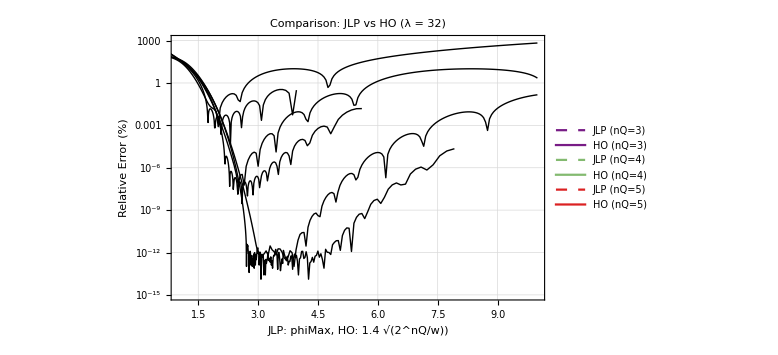

```mathematica
plotcomparisonJLPHO = CompareResultsSimple[resultsJLP,resultsHO,nqList, 1.4]
```